# “Theoretical models of energy transfer in two-dimensional molecular assemblies”

### Obliczenia analityczne

szczegóły obliczeń w artykule: E. Bartnik and J.A. Tuszyński, Phys. Rev. E 48 (1993)

### Parametry symulacji

```mathematica
ClearAll["Global `*"];  (* czyszczenie jądra programu ze wszystkich zmiennych *)
$PrePrint=MatrixForm; (* wyświetlanie w formie macierzowej *)
```

```mathematica
nmax=65; (* wymiar przestrzeni Hilberta *)
Ω=1; (* stała dla oddziaływania własnego *)
Subscript[Ω, 01]=0.9; (* stała oddziaływania dla domieszki *)
Subscript[Ω, 02]=0.95;
J=0.1; (* stała dla oddziaływania wzajemnego *)
```

### Hamiltonian H=∑_n [Ω A_n^+A_n - J A_n^+ (A_(n-1)+A_(n+1))]

```mathematica
h=Table[Which[n==m-1||n==m+1,-J,True,0]+Which[n==m,Ω,True,0],{n,nmax},{m,nmax}]; (* hamiltonian dla polimeru *)
```

### Hamiltonian H + periodyczne warunki brzegowe (PBC)

```mathematica
hsym=h;
hsym[[1,nmax]]=-J; (* periodyczne warunki brzegowe *)
hsym[[nmax,1]]=-J;
```

### Wartości własne hamiltonianu

```mathematica
eig=Eigenvalues[h]; (* widmo energii własnych hamiltonianu *)
eig2=Eigenvalues[hsym];
```

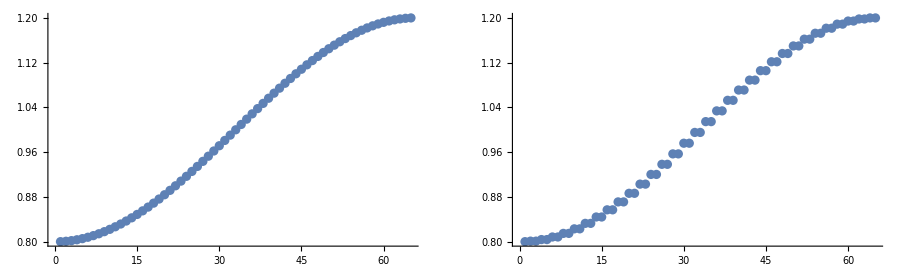

```mathematica
r1=ListPlot[Sort[eig]]; (* wykres posortowanych wartości własnych *)
r2=ListPlot[Sort[eig2]];
GraphicsGrid[{{r1,r2}},ImageSize->900]
```

### Funkcje falowe stanu podstawowego i pierwszego wzbudzonego

```mathematica
wyn=Eigensystem[h]; (* wartości własne i wektory własne *)
wyn2=Eigensystem[hsym];
```

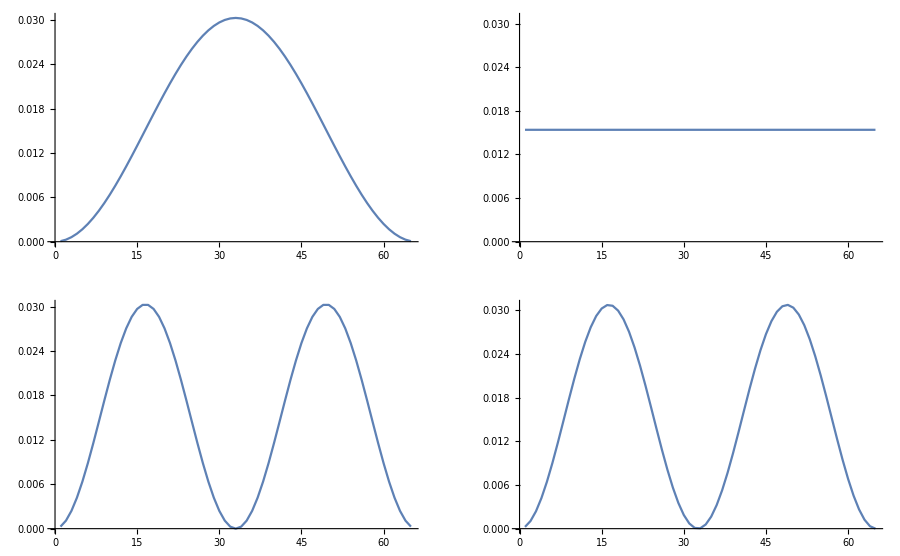

```mathematica
f1=ListPlot[Abs[wyn[[2,nmax]]^2],Joined->True,PlotRange->All] ; (* wektor własny dla stanu podstawowego, brak PBC *)
f2=ListPlot[Abs[wyn[[2,nmax-1]]^2],Joined->True,PlotRange->All] ; (* wektor własny dla pierwszego stanu wzbudzonego, brak PBC *)
f3=ListPlot[Abs[wyn2[[2,nmax]]^2],Joined->True,PlotRange->All] ; (* wektor własny dla stanu podstawowego, PBC *)
f4=ListPlot[Abs[wyn2[[2,nmax-1]]^2],Joined->True,PlotRange->All] ; (* wektor własny dla pierwszego stanu wzbudzonego, PBC *)
GraphicsGrid[{{f1,f3},{f2,f4}},ImageSize->900]
```

```mathematica
(* porównanie kolejnych wektorów własnych obu hamiltotianów *)
Manipulate[
wyn=Eigensystem[h];
wyn2=Eigensystem[hsym];
f1=ListPlot[Abs[wyn[[2,k]]^2],Joined->True,PlotRange->All] ;
f2=ListPlot[Abs[wyn2[[2,k]]^2],Joined->True,PlotRange->All] ;
GraphicsGrid[{{f1,f2}},ImageSize->900],{{k,nmax},1,nmax,1}]
```

### ciąg dalszy (5.12.2014)

```mathematica
hdom1=h;
hdom1[[(nmax+1)/2,(nmax+1)/2]]=Subscript[Ω, 01];
hdom2=h;
hdom2[[(nmax+1)/2,(nmax+1)/2]]=Subscript[Ω, 02];
```

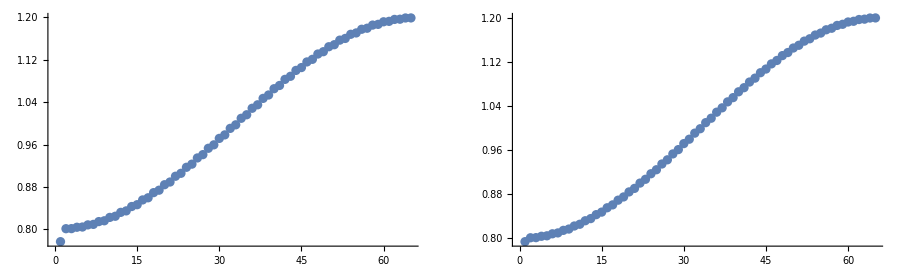

```mathematica
eig3=Eigenvalues[hdom1];
eig4=Eigenvalues[hdom2];
r3=ListPlot[Sort[eig3]];
r4=ListPlot[Sort[eig4]];
GraphicsGrid[{{r3,r4}},ImageSize->900]
```

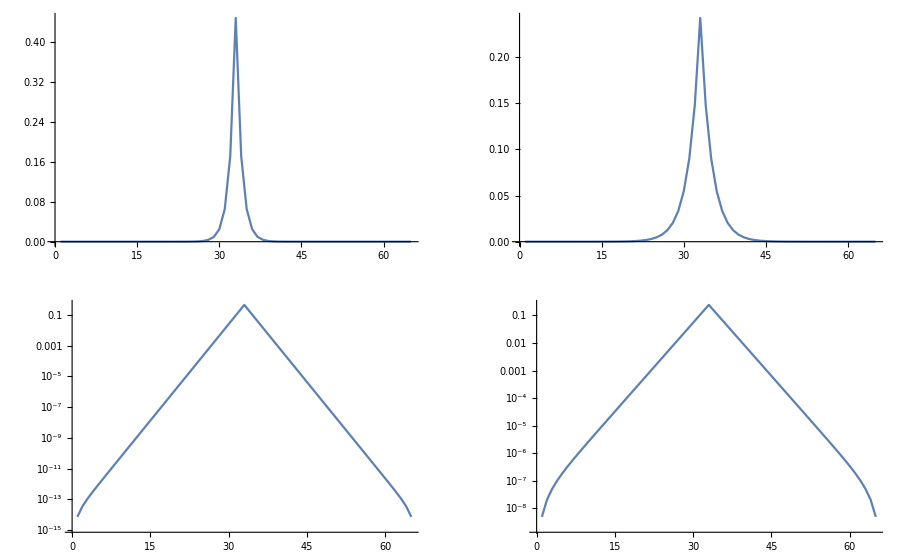

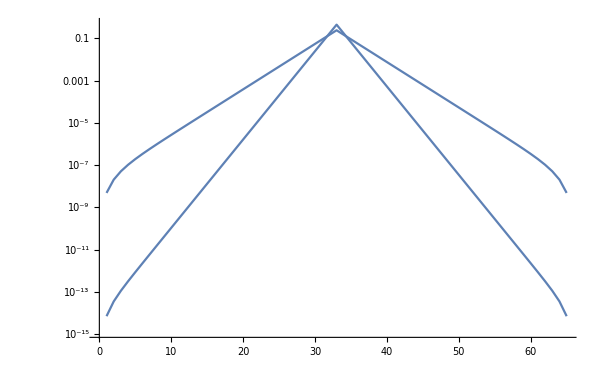

```mathematica
wyn3=Eigensystem[hdom1];
wyn4=Eigensystem[hdom2];
f5=ListPlot[Abs[wyn3[[2,nmax]]^2],Joined->True,PlotRange->All];
f6=ListLogPlot[Abs[wyn3[[2,nmax]]^2],Joined->True,PlotRange->All];
f7=ListPlot[Abs[wyn4[[2,nmax]]^2],Joined->True,PlotRange->All];
f8=ListLogPlot[Abs[wyn4[[2,nmax]]^2],Joined->True,PlotRange->All];
GraphicsGrid[{{f5,f7},{f6,f8}},ImageSize->900]
Show[{f6,f8}]
```